# 1. kviz - Računalniška orodja v matematiki

Na kvizu je skupno možno doseči 20 točk. Za vsako pravilno rešeno podnalogo dobite 1 točko. Delnih točk ni.
Rešitve pišite takoj pod navodilom ustrezne podnaloge. 

Veliko uspeha pri reševanju!

#### 1. Prepisovalna pravila

a. Definirajte prepisovalno pravilo, ki  v izrazu vse pojavitve x zamenja s klicem funkcije f na argumentu x.

```mathematica
x /.{x->f[x]}
```

1+x^4

b. Na izrazu `izraz` najprej uporabite pravilo definirano v prejšnji nalogi za funkcijo , nato pa s prepisovalnimi pravili izračunajte vrednost dobljenega izraza za x = e (x = ⅇ) in y = 1/2.

```mathematica
f[x_]:=x^4+1
```

```mathematica
izraz = Log[x] + 2y / x;
izraz/. {{x->E},{y->1/2}}
```

{1+(2 y)/ⅇ,1/x+Log[x]}

c. Definirajte prepisovalno pravilo, ki zamenja vse pojavitve  z .

```mathematica
pravilo:=x^n_:>x^(n+1)/(2 n+1)
```

d. Prepisovalno pravilo iz naloge c uporabite na funkciji ,  kolikokrat gre.

```mathematica
g[x_]:=x^-42
g[x]//.pravilo
```

1/536347102817482913555411512425352545980058003572241486357421875

e. Definiraj prepisovalna pravila, s pomočjo katerih lahko izračunate poljuben člen fibonaccijevega zaporedja, z začetkom `Fib[10]`.

#### 2. Splošno o mathematici

a. Pobrišite vrednost vseh spremenljivk, ki ste jih uporabili v prejšnji nalogi.

```mathematica
ClearAll[g,f,pravilo,izraz]
```

b. Definirajte tabelo, ki bo vsebovala numerične približke naravnega logaritma v vseh številih med 1 in 100.

```mathematica
tab =Log/@Table[i,{i, 1, 100}]
```

{0,Log[2],Log[3],Log[4],Log[5],Log[6],Log[7],Log[8],Log[9],Log[10],Log[11],Log[12],Log[13],Log[14],Log[15],Log[16],Log[17],Log[18],Log[19],Log[20],Log[21],Log[22],Log[23],Log[24],Log[25],Log[26],Log[27],Log[28],Log[29],Log[30],Log[31],Log[32],Log[33],Log[34],Log[35],Log[36],Log[37],Log[38],Log[39],Log[40],Log[41],Log[42],Log[43],Log[44],Log[45],Log[46],Log[47],Log[48],Log[49],Log[50],Log[51],Log[52],Log[53],Log[54],Log[55],Log[56],Log[57],Log[58],Log[59],Log[60],Log[61],Log[62],Log[63],Log[64],Log[65],Log[66],Log[67],Log[68],Log[69],Log[70],Log[71],Log[72],Log[73],Log[74],Log[75],Log[76],Log[77],Log[78],Log[79],Log[80],Log[81],Log[82],Log[83],Log[84],Log[85],Log[86],Log[87],Log[88],Log[89],Log[90],Log[91],Log[92],Log[93],Log[94],Log[95],Log[96],Log[97],Log[98],Log[99],Log[100]}

Solve::naqs: 0&&Log[2]&&Log[3]&&Log[4]&&Log[5]&&Log[6]&&Log[7]&&Log[8]&&Log[9]&&Log[10]&&Log[11]&&Log[12]&&Log[13]&&Log[14]&&Log[15]&&Log[16]&&Log[17]&&Log[18]&&Log[19]&&Log[20]&&Log[21]&&Log[22]&&Log[23]&&Log[24]&&Log[25]&&Log[26]&&Log[27]&&Log[28]&&Log[29]&&Log[30]&&Log[31]&&Log[32]&&Log[33]&&Log[34]&&Log[35]&&Log[36]&&Log[37]&&Log[38]&&Log[39]&&Log[40]&&Log[41]&&Log[42]&&Log[43]&&Log[44]&&Log[45]&&Log[46]&&Log[47]&&Log[48]&&Log[49]&&Log[50]&&«50» is not a quantified system of equations and inequalities.

Solve[{0,Log[2],Log[3],Log[4],Log[5],Log[6],Log[7],Log[8],Log[9],Log[10],Log[11],Log[12],Log[13],Log[14],Log[15],Log[16],Log[17],Log[18],Log[19],Log[20],Log[21],Log[22],Log[23],Log[24],Log[25],Log[26],Log[27],Log[28],Log[29],Log[30],Log[31],Log[32],Log[33],Log[34],Log[35],Log[36],Log[37],Log[38],Log[39],Log[40],Log[41],Log[42],Log[43],Log[44],Log[45],Log[46],Log[47],Log[48],Log[49],Log[50],Log[51],Log[52],Log[53],Log[54],Log[55],Log[56],Log[57],Log[58],Log[59],Log[60],Log[61],Log[62],Log[63],Log[64],Log[65],Log[66],Log[67],Log[68],Log[69],Log[70],Log[71],Log[72],Log[73],Log[74],Log[75],Log[76],Log[77],Log[78],Log[79],Log[80],Log[81],Log[82],Log[83],Log[84],Log[85],Log[86],Log[87],Log[88],Log[89],Log[90],Log[91],Log[92],Log[93],Log[94],Log[95],Log[96],Log[97],Log[98],Log[99],Log[100]}]

c.  Iz tabele v nalogi b. izberite zgolj tiste vrednosti, ki imajo na mestu desetin (prvo decimalno mesto) praštevilo.

d. Definirajte anonimno funkcijo enega argumenta, ki  izračuna kub argumenta in prišteje argument in jo uporabite na zgoraj dobljenem seznamu.

e. Seznam iz prejšnje naloge zaokrožite navzdol in seštejte vsa tista števila, ki so soda.

#### 3. Analiza z mathematico

a. Definirajte funkcijo .

```mathematica
f[x_]:=5 ⅇ^x x^2
```

b. Izračunajte definicijsko območje funkcije .

```mathematica
FunctionDomain[f[x],x]
```

True

c. Izračunajte zalogo vrednosti funkcije .

```mathematica
FunctionRange[f[x],x,y]
```

y≥0

d. Izračunajte limite funkcije  na robovih definicijskega območja.

```mathematica
Limit[f[x], x->-1/50,Direction->"FromAbove"]
Limit[f[x], x->-1/50,Direction->"FromBelow"]
```

1/(500 ⅇ^(1/50))

1/(500 ⅇ^(1/50))

e. Izračunajte odvod funkcije .

```mathematica
f'[x]
```

10 ⅇ^x x+5 ⅇ^x x^2

f. Izračunajte lokalne ekstreme funkcije  (določi tudi ali gre za lokalni minimum oz. maksimum).

g. Izračunajte intervale naraščanja in padanja funkcije .

```mathematica
Reduce[f'[x]>0, x]
Reduce[f'[x]<0, x]
```

x<-2||x>0

-2<x<0

h. Narišite graf funkcije  na intervalu [-1, 2].

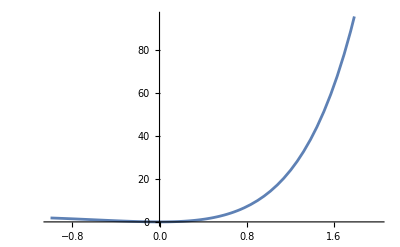

```mathematica
Plot[f[x],{x,-1,2}]
```

i. Določite intervale konveksnosti in konkavnosti funkcije .

j. Na 3 decimalke natančno izračunajte volumen vrtenine , ki jo dobimo, če graf funkcije  zavrtimo okoli  osi na intervalu [-3, 0]. Vrtenino tudi narišite.

```mathematica
Integrate[2 Pi x(f[x]), {x,-3,0}]
```

10 (-6+78/ⅇ^3) π

```mathematica
RevolutionPlot3D[f[x],{x,-3,0},RevolutionAxis->{1, 0, 0}]
```

-Graphics3D-